```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec 3.4 zero twist angle with varing lattice mismatch

## AA stacking triangle Eq.S11

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAA[x_,y_,λ_]=  Cos[(4 π (x))/(√3 λ)]+2 Cos[(2  π (x))/(√3 λ)] Cos[(2  π y)/λ]
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
γ=π/2
```

π/2

```mathematica
λ=p as/(p-1)

(*λ is moire wavelength, distance between AA point
as is lattice constant of substrate*)
```

(as p)/(-1+p)

```mathematica
f0[x_,y_,as_,p_]=Simplify[fAA[x Cos[γ]-y Sin[γ],y Cos[γ]+x Sin[γ],λ]]
```

2 Cos[(2 (-1+p) π x)/(as p)] Cos[(2 (-1+p) π y)/(√3 as p)]+Cos[(4 (-1+p) π y)/(√3 as p)]

```mathematica
nRf0[x_,y_,as_,R_,p_]=f0[x R,y R,as,p]
```

2 Cos[(2 (-1+p) π R x)/(as p)] Cos[(2 (-1+p) π R y)/(√3 as p)]+Cos[(4 (-1+p) π R y)/(√3 as p)]

```mathematica
nRnasnareauf0[x_,y_,r_,p_]=Simplify[nRf0[x,y,as,r*as*p,p]]
```

2 Cos[2 (-1+p) π r x] Cos[(2 (-1+p) π r y)/(√3)]+Cos[(4 (-1+p) π r y)/(√3)]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

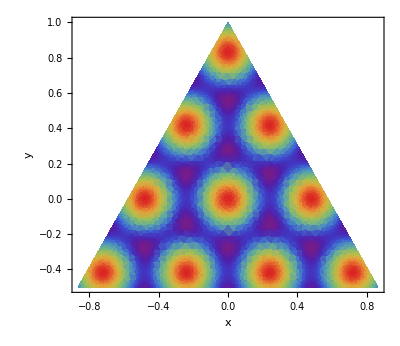

```mathematica
DensityPlot[nRnasnareauf0[x,y,12Sqrt[3],0.9],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
AAtri[r_,p_]=FullSimplify[Integrate[nRnasnareauf0[x,y,r,p]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] /triarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(Sin[((-1+p) π r)/(√3)] (6 (-1+p) π r Cos[((-1+p) π r)/(√3)]+√3 Sin[√3 (-1+p) π r]))/(√3 (-1+p)^2 π^2 r^2)

time used 0.42935543 mins

```mathematica
ToMatlab[AAtri[r,p]]
```

3.^(-1/2).*((-1)+p).^(-2).*pi.^(-2).*r.^(-2).*sin(3.^(-1/2).*((-1) ...
  +p).*pi.*r).*(6.*((-1)+p).*pi.*r.*cos(3.^(-1/2).*((-1)+p).*pi.*r)+ ...
  3.^(1/2).*sin(3.^(1/2).*((-1)+p).*pi.*r));

## AB stacking triangle Eq.S12

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAB[x_,y_,λ_]=  Cos[(4 π (x-λ/(√3)))/(√3 λ)]+2 Cos[(2  π (x-λ/(√3)))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
γ=π/2
```

π/2

```mathematica
λ=p as/(p-1)

(*λ is moire wavelength, distance between AA point
as is lattice constant of substrate*)
```

(as p)/(-1+p)

```mathematica
f0[x_,y_,as_,p_]=fAB[x Cos[γ]-y Sin[γ],y Cos[γ]+x Sin[γ],λ]
```

2 Cos[(2 (-1+p) π x)/(as p)] Cos[(2 (-1+p) π (-(as p)/(√3 (-1+p))-y))/(√3 as p)]+Cos[(4 (-1+p) π (-(as p)/(√3 (-1+p))-y))/(√3 as p)]

```mathematica
nRf0[x_,y_,as_,R_,p_]=f0[x R,y R,as,p]
```

2 Cos[(2 (-1+p) π R x)/(as p)] Cos[(2 (-1+p) π (-(as p)/(√3 (-1+p))-R y))/(√3 as p)]+Cos[(4 (-1+p) π (-(as p)/(√3 (-1+p))-R y))/(√3 as p)]

```mathematica
nRnasnareauf0[x_,y_,r_,p_]=Simplify[nRf0[x,y,as,r*as*p,p]]
```

2 Cos[2 (-1+p) π r x] Cos[2/3 π (1+√3 (-1+p) r y)]+Cos[4/3 π (1+√3 (-1+p) r y)]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

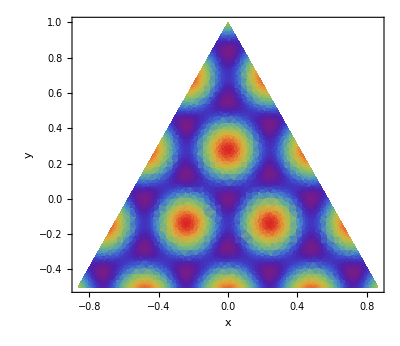

```mathematica
DensityPlot[nRnasnareauf0[x,y,12Sqrt[3],0.9],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic]
```

```mathematica
$Assumptions=r>0&&0≤θ&&p>0&&x∈Reals&&y∈Reals
```

r>0&&0≤θ&&p>0&&x∈ℝ&&y∈ℝ

```mathematica
t1=AbsoluteTime[];
ABtriUnnormalized[r_,p_]=Simplify[Integrate[nRnasnareauf0[x,y,r,p]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] ]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

(3 (√3 (-1+6 (-1+p) π r) Cos[(2 (-1+p) π r)/(√3)]+√3 Cos[(4 (-1+p) π r)/(√3)]-3 (1+2 (-1+p) π r+2 Cos[(2 (-1+p) π r)/(√3)]) Sin[(2 (-1+p) π r)/(√3)]))/(16 (-1+p)^2 π^2 r^2)

time used 1.48952439 mins

```mathematica
ABtri[r_,p_]=FullSimplify[ABtriUnnormalized[r,p]/triarea ]
```

(√3 (-1+6 (-1+p) π r) Cos[(2 (-1+p) π r)/(√3)]+√3 Cos[(4 (-1+p) π r)/(√3)]-3 (1+2 (-1+p) π r+2 Cos[(2 (-1+p) π r)/(√3)]) Sin[(2 (-1+p) π r)/(√3)])/(4 √3 (-1+p)^2 π^2 r^2)

```mathematica
ToMatlab[ABtri[r,p]]
```

(1/4).*3.^(-1/2).*((-1)+p).^(-2).*pi.^(-2).*r.^(-2).*(3.^(1/2).*(( ...
  -1)+6.*((-1)+p).*pi.*r).*cos(2.*3.^(-1/2).*((-1)+p).*pi.*r)+3.^( ...
  1/2).*cos(4.*3.^(-1/2).*((-1)+p).*pi.*r)+(-3).*(1+2.*((-1)+p).* ...
  pi.*r+2.*cos(2.*3.^(-1/2).*((-1)+p).*pi.*r)).*sin(2.*3.^(-1/2).*(( ...
  -1)+p).*pi.*r));